```mathematica
G = 1/(s^2(τ s + 1))
```

1/(s^2 (1+s τ))

```mathematica
H = h s + 1
```

1+h s

```mathematica
K = kp +kd s+ kdd s^2
```

kp+kd s+kdd s^2

```mathematica
data={h->0.1, τ->0.1, kp->0.2, kd->0.7, kdd->0};
```

```mathematica
gammaFF = 1/H * (1+G K)/(1+G K)//Simplify
```

1/(1+h s)

```mathematica
gamma = 1/H * (G K)/(1+G K)//Simplify
```

(kp+s (kd+kdd s))/((1+h s) (kp+s (kd+s (1+kdd+s τ))))

```mathematica
gammaFFTF = TransferFunctionModel[gammaFF,s]
```

1/(1+h s)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11111FalseFalseFalseAutomaticNoneAutomatic

```mathematica
gammaTF = TransferFunctionModel[gamma,s]
```

(kp+s (kd+kdd s))/((1+h s) (kp+s (kd+s (1+kdd+τ s))))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s11$CellContext`kp11FalseFalseFalseAutomaticNoneAutomatic

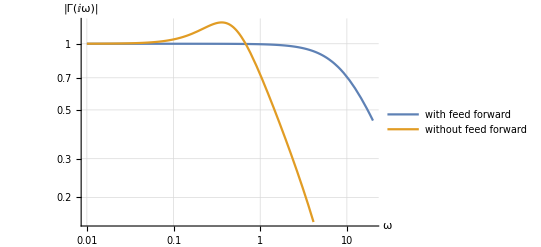

```mathematica
p1 = Abs[gammaFF/.data/.s->ⅈ ω];
p2= Abs[gamma/.data/.s->ⅈ ω];
LogLogPlot[{p1,p2},{ω,0.01,20},PlotRange->Automatic, GridLines->Automatic, PlotLegends->{"with feed forward", "without feed forward"},
AxesLabel->{"ω","|Γ(ⅈω)|"}]
```

```mathematica
Solve[{Abs[Denominator[gamma/.data/.s->ⅈ ω]] == 0},ω]
```

{{ω→-0.286075+0.366002 ⅈ},{ω→0.+9.268 ⅈ},{ω→0.+10. ⅈ},{ω→0.286075+0.366002 ⅈ}}

```mathematica
Denominator[gamma/.data/.s->ⅈ ω]//Simplify
```

(1+(0.+0.1 ⅈ) ω) (0.2+(0.+0.7 ⅈ) ω-ω^2-(0.+0.1 ⅈ) ω^3)

### TF for first order model

```mathematica
gammaFirstOrder=TransferFunctionModel[1/(s(h s -kp)-s),s]
```

1/(-s+s (-kp+h s))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s111$CellContext`s1FalseFalseFalseAutomaticNoneAutomatic

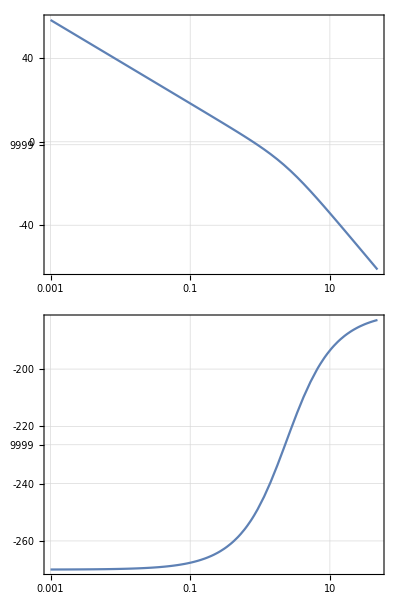

```mathematica
BodePlot[gammaFirstOrder/.data, GridLines->Automatic]
```